## Tanks Problem

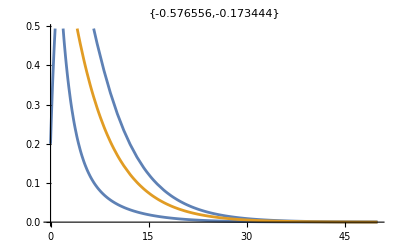

```mathematica
A=({{-5/10, 1.0/20}, {5/10, -5/20}}) ; y0={1.2,0.2};
TMax=50;
ySol=NDSolveValue[{y'[t]==A.y[t],y[0]==y0},y,{t, 0, TMax}];
Plot[{ySol[t],E^(-0.173 t)},{t,0, TMax},PlotLabel->Eigenvalues[A]]
LogPlot[{ySol[t],E^(-0.173 t)},{t,0, TMax},PlotLabel->Eigenvalues[A]];
```

## Circuit Problem

The matrix for our LRC circuit is
	(0 | 1
-1/(L C) | -R/L) 
Looking at eigenvalues and simulations.   For R=10, C=0.5, and L=0.5

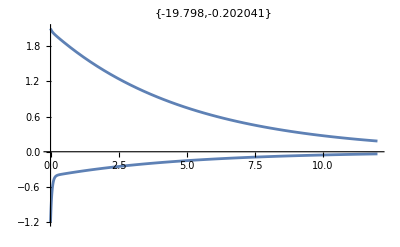

```mathematica
A=({{0, 1}, {-1/0.5^2, -10/0.5}}) ; y0={2.1,-1.2};
TMax=12;
ySol=NDSolveValue[{y'[t]==A.y[t],y[0]==y0},y,{t, 0, TMax}];
Plot[ySol[t],{t,0, TMax},PlotLabel->Eigenvalues[A]]
```

If we make R smaller say R=1 we get wiggles. For R=1, C=0.5, and L=0.5

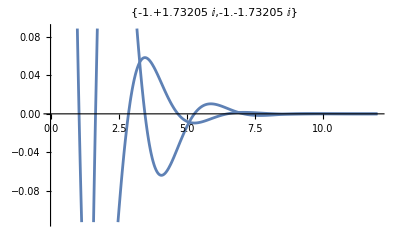

```mathematica
A=({{0, 1}, {-1/0.5^2, -1/0.5}}) ; y0={2.1,-1.2};
TMax=12;
ySol=NDSolveValue[{y'[t]==A.y[t],y[0]==y0},y,{t, 0, TMax}];
Plot[ySol[t],{t,0, TMax},PlotLabel->Eigenvalues[A]]
```